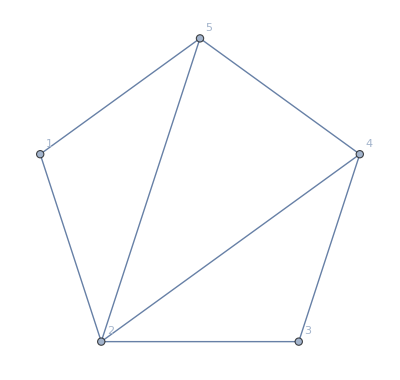

```mathematica
g=EdgeAdd[Graph[CycleGraph[5],VertexLabels->"Name"],{2<->4,2<->5}]
```

```mathematica
ChromaticPolynomial[g,x]
```

8 x-20 x^2+18 x^3-7 x^4+x^5

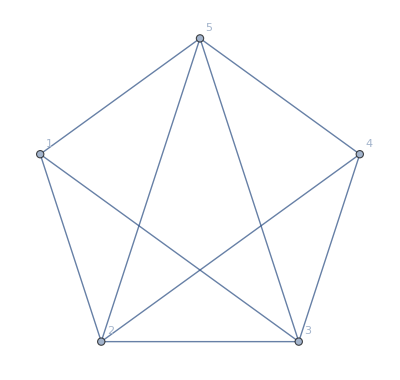

```mathematica
h=EdgeAdd[g,{3<->1,3<->5}]
```

```mathematica
ChromaticPolynomial[h,x]/ChromaticPolynomial[g,x]/.x->4
```

1/4

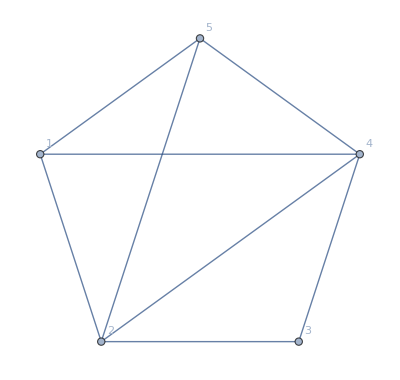

```mathematica
f=EdgeAdd[g,{1<->4}]
```

```mathematica
ChromaticPolynomial[f,x]/ChromaticPolynomial[g,x]/.x->4
```

1/2